```mathematica
signatures = {{{2,2}}->{{4,2}},{{2,2}}->{{3,2}},{{2,2}}->{{2,2}}};
maxElements={6,6,6};
connectednesses={All,All,All};
```

```mathematica
rule=MapThread[ResourceFunction["RandomWolframModel"],{signatures,maxElements,connectednesses}]
```

{{{1,2},{2,3}}→{{1,4},{4,1},{1,3},{2,1}},{{1,2},{2,3}}→{{1,2},{1,4},{5,1}},{{1,2},{2,1}}→{{1,2},{2,3}}}

```mathematica
evolution=ResourceFunction["WolframModel"][rule,Automatic,7, "EventOrderingFunction"->"Random"]
```

WolframModelEvolutionObject[…]

```mathematica
evolution["AllEventsRuleIndices"]
```

{3,2,1,1,2,3,1,2,1,2,2,2,1,1}

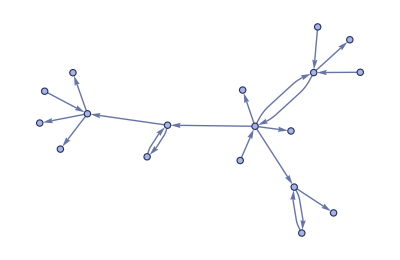

```mathematica
evolution["FinalStatePlot"]
```